## Study the behavior of the oscillator frequencies ω_1 and ω_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
S[I_,j_]:=(2I-1-2j)/(2I-1);
SP[I_,j_]:=(2j-2I-1)/(2j-1);
T[j_,γ_]:=1/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]);
TP[j_,γ_]:=1/(j(j+1))2Sqrt[3]Sin[γ];
```

### Create the omega sub-terms

### Nuclear total spin -> i Single-particle spin -> j

```mathematica
st1[i_,j_,a1_,a3_]:=(2i-1)(a3-a1)+2*j*a1;
st2[i_,j_,a1_,a2_]:=(2i-1)(a2-a1)+2*j*a1;
st3[i_,j_,a1_,a3_,v_,γ_]:=(2j-1)(a3-a1)+2*i*a1+v*(2j-1)/(j(j+1))√3(√3 Cos[γ]+Sin[γ]);
st4[i_,j_,a1_,a2_,v_,γ_]:=(2j-1)(a2-a1)+2i*a1+v*(2j-1)/(j(j+1))2 √3*Sin[γ];
```

```mathematica
omega1[i_,j_,a1_,a2_,a3_]:=(st1[i,j,a1,a3]*st2[i,j,a1,a2])^(1/2);
omega2[i_,j_,a1_,a2_,a3_,v_,γ_]:=(st3[i,j,a1,a3,v,γ])^(1/2)*(st4[i,j,a1,a2,v,γ])^(1/2);
```

### Numerical interpretation

```mathematica
j0=13/2;
A1=0.05;
A2=2*A1;
A3=5*A1;
V=3;
γ=25*π/180;
```

```mathematica
intersectionPoint1=Select[Flatten[Values@Solve[omega1[x,j0,A1,A2,A3]==omega2[x,j0,A1,A2,A3,V,γ],{x}]],Positive]
intersectionPoint2=Select[Flatten[Values@Solve[omega1[x,j0,A1,A3,A2]==omega2[x,j0,A1,A3,A2,V,γ],{x}]],Positive];
```

{23.8482}

```mathematica
intersectionPoint2[[1]]
```

26.199

## Create numerical data

### Omega1

```mathematica
Print[{A1,A1*S[spin,j0]}/.{spin->35/2}]
```

{0.05,0.0308824}

### Omega2

```mathematica
Print[{A1,SP[spin,j0]*A1-V*TP[j0,γ],SP[spin,j0]*A1-V*T[j0,γ]}/.{spin->35/2}]
```

{0.05,-0.185925,-0.308198}

```mathematica
data1=Table[{i,omega1[i,j0,A1,2A1,5A1]},{i,3/2,85/2,2}];
data2=Table[{i,omega2[i,j0,A1,2A1,5A1,V,γ]},{i,3/2,85/2,2}];
data3=Table[{i,omega1[i,j0,A1,5A1,2A1]},{i,3/2,85/2,2}];
data4=Table[{i,omega2[i,j0,A1,5A1,2A1,V,γ]},{i,3/2,85/2,2}];
fig1=ListPlot[{data1,data2},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,FrameStyle->Directive[Black, Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},AspectRatio->0.8,FrameLabel->{"I [ℏ]","ω [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{"ω_1","ω_2"},{0.4,0.85}],PlotRange->{Full,Full},ImageSize->380];
fig2=ListPlot[{data3,data4},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,FrameStyle->Directive[Black, Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},AspectRatio->0.8,FrameLabel->{"I [ℏ]","ω [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{"ω_1","ω_2"},{0.4,0.85}],PlotRange->{Full,Automatic},ImageSize->380];
obg1=Show[{fig1,Graphics[{Thickness[0.009],Dashed,Black,Line[{{j0,-1},{j0,15}}]}],Graphics[{Gray,HatchFilling[-1],Opacity[0.6],Rectangle[{-1,-1},{13/2,10}]}],Graphics[{Orange,Opacity[0.05],Rectangle[{13/2,-1},{50,10}]}],Graphics[Inset[Style["I ≤ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.08,0.6}]]],Graphics[Inset[Style["I ≥ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.3,0.6}]]],Graphics[{Red,Thickness[0.009],DotDashed,Line[{{intersectionPoint1[[1]],-1},{intersectionPoint1[[1]],10}}]}]}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/omega-1-2-frequencies-1.pdf",obg1,ImageResolution->800];
obg2=Show[{fig2,Graphics[{Thick,Dashed,Magenta,Line[{{j0,-1},{j0,15}}]}]}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/omega-1-2-frequencies-2.pdf",obg2,ImageResolution->800];
obg1
```

-Graphics-

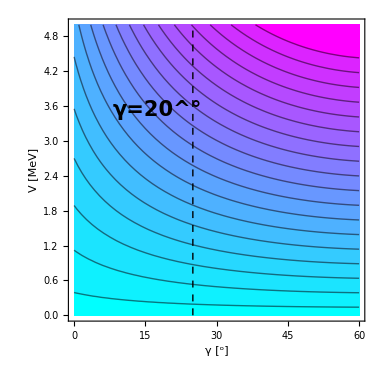

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
cp=ContourPlot[omega2[35/2,j0,A1,2A1,5A1,x,y*π/180],{y,0,60},{x,0,5},Contours->18(*ContourLabels->(Text[Style[#3,Red,Bold,13],{#1,#2},Background->None]&)*),ColorFunction->CoolColor,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"γ [^o]","V [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},ImageSize->380,PlotRangePadding->0,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->300,LegendFunction->"Frame",LegendMargins->2,LegendLabel->"ω_2 [MeV]"],Right]];
obj=Show[cp,Graphics[{Black,Thick,Dashed,Line[{{25,0},{25,5}}]}],Graphics[Inset[Style["γ=20^°",Black,Bold,FontFamily->"Arial",21],Scaled[{0.3,0.7}]]]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/omega-2-gamma-V.pdf",obj,ImageResolution->800];
obj
```

```mathematica
.b4
```

.b4